{{y→Function[{x},ⅇ^-x C[1]+ⅇ^(11 x) C[2]]}}

{{y→InterpolatingFunction[…]}}

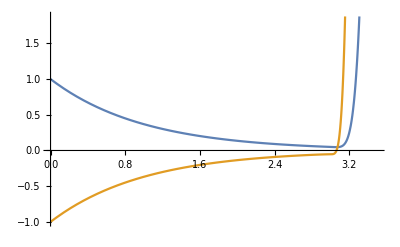

```mathematica
sol=DSolve[y''[x]-10*y'[x]-11y[x]==0,y,x]


s=NDSolve[{y''[x]-10*y'[x]-11y[x]==0,y[0]==1,y'[0]==-1},y,{x,0,3}]



Plot[Evaluate[{y[x],y'[x]}/.s],{x,0,3.5},PlotStyle->Automatic]
```